## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p385/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.016 ,0.01, 0.008 ,0.0063 ,0.005 ,0.00385, 0.0031 ,0.0028, 0.0025 ,0.0022 ,0.002 ,0.0018,0.001 ,0.00067, 0.0005 ,0.0004, 0.00033,0.00025 ,0.00018 ,0.00014 ,0.00011 ,0.0001};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000,0.00040000,0.00033000,0.00025000,0.00018000,0.00014000,0.00011000,0.00010000,0.00008700,0.00007700}

```mathematica
wtlist={0.,80000.,90000.,100000.};
```

```mathematica
wtlist={0.,50000.,60000.,70000.,80000.,90000.,100000.};
```

```mathematica
wtliststring=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlist
```

{0.00,80000.00,90000.00,100000.00}

```mathematica
wtlistLongest={10000.,10000.,10000.,10000.,10000.,10000.,10000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.};
```

```mathematica
wtlistLongestString=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.8500_T",Tstring[[Length[Tlist]-1]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,Length[wtlist]}],{idx,0,2}];
```

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.8500_T",Tstring[[16]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,Length[wtlist]}],{idx,0,2}];
```

```mathematica
timeLongest=Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8500_T",Tstring[[16]],"_waitingTime",wtliststring[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,Length[wtlist]}];
```

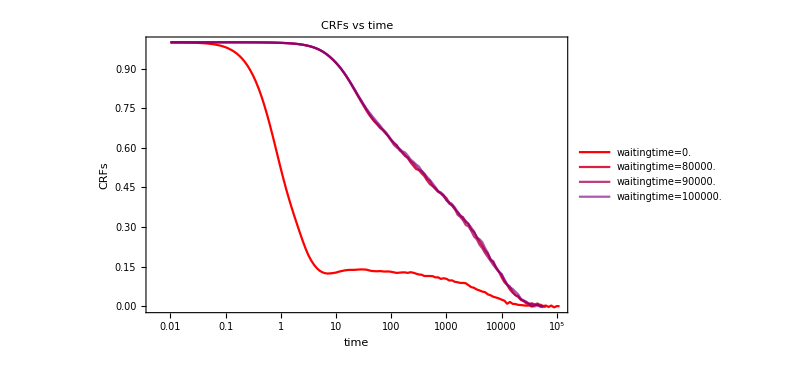

```mathematica
CRFswaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[SISF[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]-5}],{wt,Length[wtlist]}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,Length[wtlist]}],PlotRange->All]
```

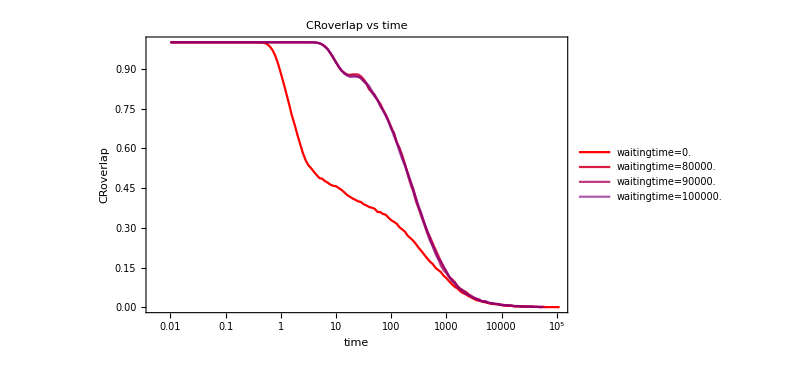

```mathematica
CRoverlapwaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[overlap[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]-5}],{wt,4}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,4}],PlotRange->{All,{0,1}}]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.8500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
Length[Tlist]
```

26

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.8500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
CRoverlapMean=Table[Table[Mean[Table[overlap[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
overlapMean=Table[Table[Mean[Table[overlap[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISFMean=Table[Table[Mean[Table[SISF[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFMean=Table[Table[Mean[Table[SISF[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8500_T",Tstring[[16]],"_waitingTime",wtlistLongestString[[16]],"_idx1.nc"],"Data"];time=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

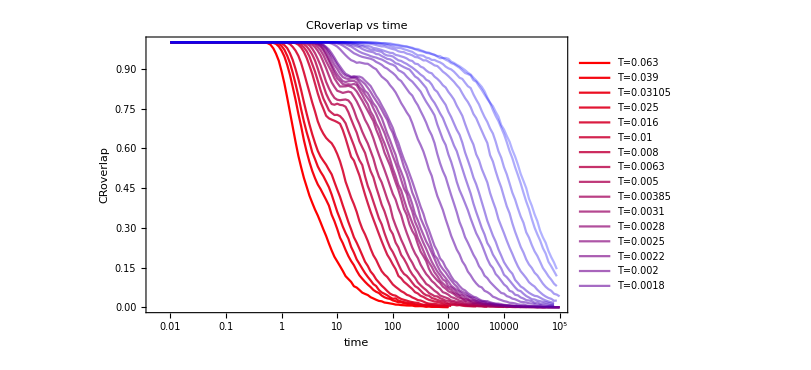

```mathematica
CRoverlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
fitCROverlapStartNum={4.545633497156052,6.972324797990245,7.688430481846143,9.342191365655887,11.359328382212755,15.816075884439703,17.103424454731552,21.189518319840886,23.81560922495133,27.8367722375015,30.685453336137705,33.82312067339929,36.55834456391838,39.51772229179588,41.89421685655501,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,80.,80.,80.,80.,80.};
```

```mathematica
fitCROverlapStartPos=Table[Position[time,_?(#>fitCROverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{45,48,49,51,53,55,56,58,59,60,61,62,63,63,64,65,65,65,65,65,65,70,70,70,70,70}

```mathematica
fitsCROverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[T,rec]]]},{rec,fitCROverlapStartPos[[T]],Length[CRoverlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,1.0>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCROverlap
```

{FittedModel[0.999939 ⅇ^(-0.515545 t^0.519302)],FittedModel[0.999966 ⅇ^(-0.353184 t^0.541758)],FittedModel[0.999971 ⅇ^(-0.2793 t^0.568154)],FittedModel[0.999978 ⅇ^(-0.222379 t^0.586029)],FittedModel[0.999987 ⅇ^(-0.161697 t^0.593373)],FittedModel[0.999993 ⅇ^(-0.0907881 t^0.646466)],FittedModel[0.999995 ⅇ^(-0.0756969 t^0.649911)],FittedModel[0.999995 ⅇ^(-0.0587052 t^0.661151)],FittedModel[0.999996 ⅇ^(-0.0469572 t^0.66898)],FittedModel[0.999996 ⅇ^(-0.0360893 t^0.677554)],FittedModel[0.999997 ⅇ^(-0.0279403 t^0.691862)],FittedModel[0.999998 ⅇ^(-0.0266328 t^0.686269)],FittedModel[0.999998 ⅇ^(-0.0223404 t^0.698644)],FittedModel[0.999998 ⅇ^(-0.0206731 t^0.696748)],FittedModel[0.999998 ⅇ^(-0.0162701 t^0.717823)],FittedModel[0.999998 ⅇ^(-0.0162733 t^0.701715)],FittedModel[0.999999 ⅇ^(-0.00704847 t^0.736315)],FittedModel[0.999999 ⅇ^(-0.00444992 t^0.741402)],FittedModel[0.999999 ⅇ^(-0.00353361 t^0.725584)],FittedModel[0.999999 ⅇ^(-0.00267254 t^0.729492)],FittedModel[0.999999 ⅇ^(-0.00188821 t^0.741303)],FittedModel[0.999999 ⅇ^(-0.0014236 t^0.733621)],FittedModel[0.999998 ⅇ^(-0.000814249 t^0.752556)],FittedModel[0.999999 ⅇ^(-0.000641544 t^0.743966)],FittedModel[0.999995 ⅇ^(-0.000330518 t^0.778901)],FittedModel[0.999998 ⅇ^(-0.000380123 t^0.754086)]}

```mathematica
tauCROverlapfits=Table[fitsCROverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{3.5816,6.82841,9.43977,13.0053,21.5555,40.9069,53.0556,72.844,96.7288,134.636,176.108,196.975,230.685,261.696,310.253,353.828,836.628,1485.58,2393.55,3366.77,4726.53,7589.61,12735.1,19568.5,29435.,34307.9}

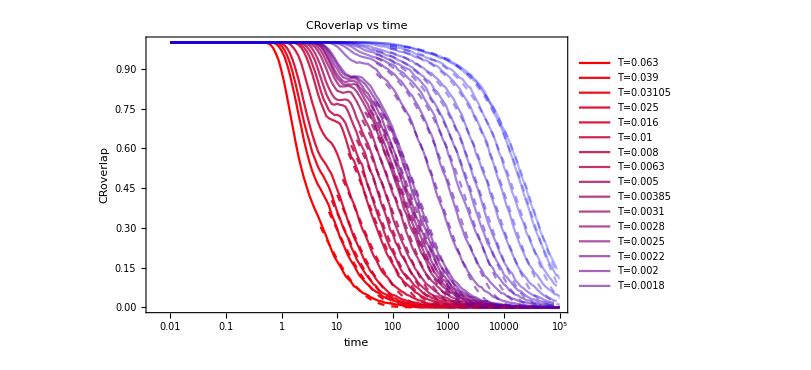

```mathematica
Show[CRoverlapPlot,Table[LogLinearPlot[fitsCROverlap[[T]][x],{x,time[[fitCROverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

### overlap

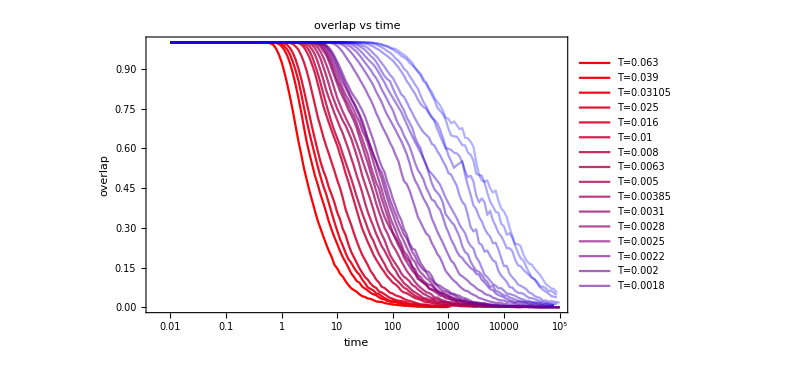

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
Log10[time[[66]]]
```

1.74997

```mathematica
fitOverlapStartPos=fitCROverlapStartPos
```

{45,48,49,51,53,55,56,58,59,60,61,62,63,63,64,65,65,65,65,65,65,70,70,70,70,70}

```mathematica
fitsOverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,1.0>G>0,τ>0.5}},{G,τ,β,c},t],{T,Length[Tlist]}];
```

```mathematica
fitsOverlap
```

{FittedModel[0.999926 ⅇ^(-0.536417 t^0.539512)],FittedModel[0.999944 ⅇ^(-0.427175 t^0.526454)],FittedModel[0.999955 ⅇ^(-0.360978 t^0.542748)],FittedModel[0.999965 ⅇ^(-0.30024 t^0.559009)],FittedModel[0.999974 ⅇ^(-0.2158 t^0.589524)],FittedModel[0.999986 ⅇ^(-0.171089 t^0.573924)],FittedModel[0.999986 ⅇ^(-0.155934 t^0.565231)],FittedModel[0.999986 ⅇ^(-0.126934 t^0.57892)],FittedModel[0.999991 ⅇ^(-0.0998423 t^0.603582)],FittedModel[0.999992 ⅇ^(-0.0887162 t^0.596528)],FittedModel[0.999993 ⅇ^(-0.0940425 t^0.554434)],FittedModel[0.999994 ⅇ^(-0.0747368 t^0.598773)],FittedModel[0.999994 ⅇ^(-0.0678998 t^0.602471)],FittedModel[0.999995 ⅇ^(-0.0603019 t^0.608097)],FittedModel[0.999993 ⅇ^(-0.0712109 t^0.560935)],FittedModel[0.999994 ⅇ^(-0.0623907 t^0.573783)],FittedModel[0.999997 ⅇ^(-0.0345885 t^0.593696)],FittedModel[0.999999 ⅇ^(-0.0240833 t^0.604994)],FittedModel[0.999999 ⅇ^(-0.0250294 t^0.561273)],FittedModel[0.999999 ⅇ^(-0.0170804 t^0.592325)],FittedModel[0.999999 ⅇ^(-0.0173652 t^0.570415)],FittedModel[0.999999 ⅇ^(-0.0169391 t^0.532105)],FittedModel[0.999999 ⅇ^(-0.00921207 t^0.574582)],FittedModel[1. ⅇ^(-0.0134022 t^0.504298)],FittedModel[1. ⅇ^(-0.00689331 t^0.55846)],FittedModel[1. ⅇ^(-0.00677154 t^0.546929)]}

```mathematica
tauOverlapfits=Table[fitsOverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{3.1723,5.03112,6.53628,8.6049,13.4784,21.6783,26.7818,35.3538,45.4896,58.014,71.0811,76.0834,86.8763,101.324,111.073,125.86,289.048,473.014,713.546,963.843,1219.08,2130.59,3489.99,5172.79,7423.28,9254.43}

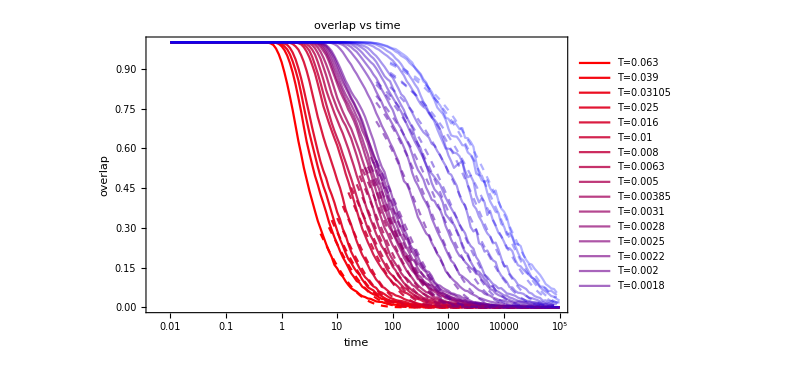

```mathematica
Show[overlapPlot,Table[LogLinearPlot[fitsOverlap[[T]][x],{x,time[[fitOverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

Show::gcomb: Could not combine the graphics objects in Show[CRoverlapfitST,CRoverlapLTPlot,{}].

#### CRSISF

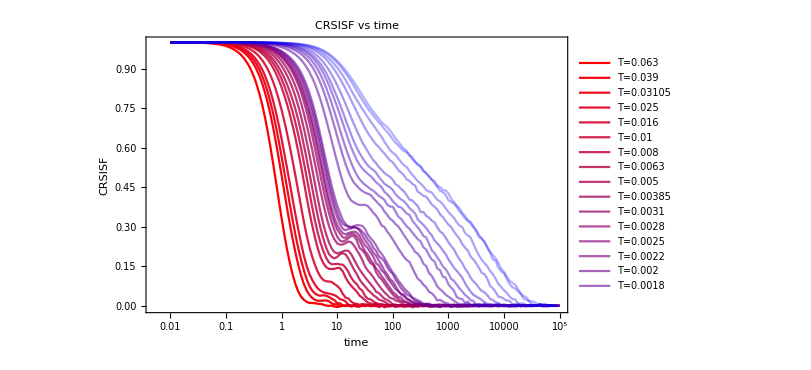

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[T,rec]]},{rec,Length[CRSISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitCRSISFStartNum={4.337072420050368,7.194205862609111,7.931187148870541,11.041221920722247,12.41437888222547,15.092266119370647,17.301989581024966,20.62319820061897,23.639957937652536,28.730316073927884,33.577461003101725,36.300996533057514,40.01970511999825,41.61110332104524,46.77333136987734,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,80.,80.,80.,80.,80.};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{44,49,49,52,53,55,56,58,59,61,62,63,64,64,65,66,66,66,66,66,66,70,70,70,70,70}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[T,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[CRSISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.561604 ⅇ^(-1.12214 t^0.890383)],FittedModel[0.561625 ⅇ^(-0.664609 t^0.888215)],FittedModel[0.59677 ⅇ^(-0.489243 t^0.898811)],FittedModel[0.59771 ⅇ^(-0.360489 t^0.8992)],FittedModel[0.58893 ⅇ^(-0.274403 t^0.888606)],FittedModel[0.501248 ⅇ^(-0.144193 t^0.892447)],FittedModel[0.478341 ⅇ^(-0.110853 t^0.898794)],FittedModel[0.511187 ⅇ^(-0.119157 t^0.807516)],FittedModel[0.405287 ⅇ^(-0.0588925 t^0.899431)],FittedModel[0.406622 ⅇ^(-0.0448733 t^0.897256)],FittedModel[0.447637 ⅇ^(-0.0370789 t^0.897246)],FittedModel[0.429279 ⅇ^(-0.0326504 t^0.898543)],FittedModel[0.43632 ⅇ^(-0.0353163 t^0.844263)],FittedModel[0.456359 ⅇ^(-0.027013 t^0.893645)],FittedModel[0.426028 ⅇ^(-0.0210017 t^0.899696)],FittedModel[0.450952 ⅇ^(-0.0212104 t^0.887575)],FittedModel[0.474974 ⅇ^(-0.0143697 t^0.822042)],FittedModel[0.482521 ⅇ^(-0.00891813 t^0.823415)],FittedModel[0.492746 ⅇ^(-0.00761164 t^0.791896)],FittedModel[0.530813 ⅇ^(-0.00858239 t^0.747604)],FittedModel[0.56397 ⅇ^(-0.0114246 t^0.673489)],FittedModel[0.550966 ⅇ^(-0.00715308 t^0.692116)],FittedModel[0.599995 ⅇ^(-0.00744227 t^0.648271)],FittedModel[0.599999 ⅇ^(-0.00480745 t^0.670267)],FittedModel[0.6 ⅇ^(-0.00235083 t^0.716105)],FittedModel[0.6 ⅇ^(-0.00220746 t^0.717626)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.8786,1.58403,2.21528,3.11014,4.28562,8.7582,11.5562,13.9348,23.3058,31.7959,39.3313,45.0726,52.4653,56.897,73.2474,76.8102,174.354,308.531,473.425,580.793,765.115,1258.7,1918.81,2873.75,4687.51,5026.2}

```mathematica
Length[TlistLongest]
```

0

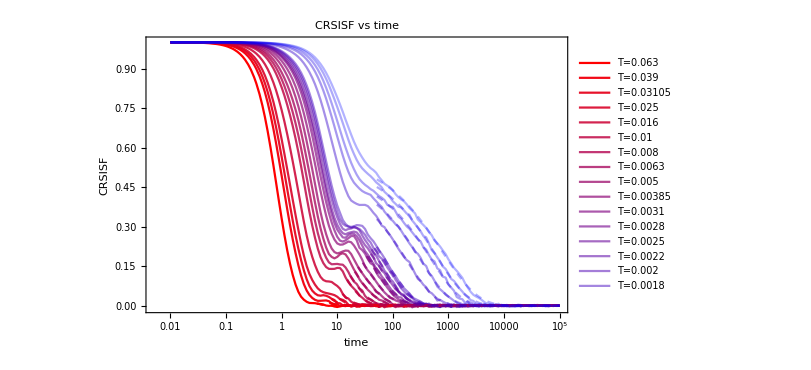

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

Show::gcomb: Could not combine the graphics objects in Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,{}].

#### SISF

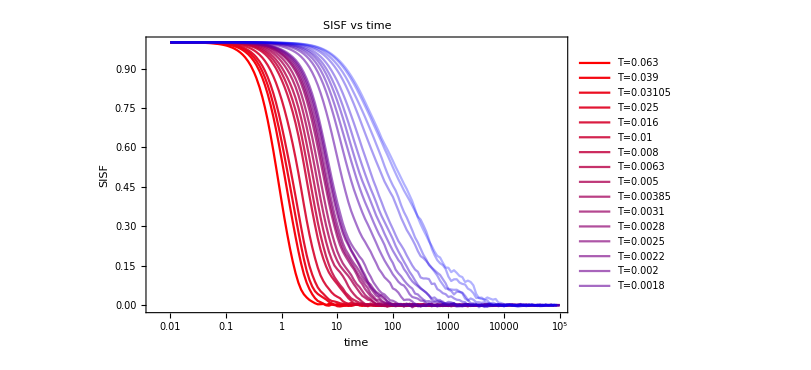

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[T,rec]]},{rec,Length[SISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

```mathematica
time[[40]]
```

2.82

```mathematica
fitSISFStartPos=fitCRSISFStartPos-5
```

{39,44,44,47,48,50,51,53,54,56,57,58,59,59,60,61,61,61,61,61,61,65,65,65,65,65}

```mathematica
fitsSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[T,rec]]]},{rec,fitSISFStartPos[[T]],Length[SISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsSISF
```

{FittedModel[0.964593 ⅇ^(-1.41191 t^0.875504)],FittedModel[0.984679 ⅇ^(-1.08658 t^0.897084)],FittedModel[0.65112 ⅇ^(-0.692349 t^0.897776)],FittedModel[0.863445 ⅇ^(-1.0317 t^0.639523)],FittedModel[0.449592 ⅇ^(-0.360708 t^0.87326)],FittedModel[0.65504 ⅇ^(-0.265978 t^0.899231)],FittedModel[0.560542 ⅇ^(-0.233263 t^0.888657)],FittedModel[0.816716 ⅇ^(-0.203832 t^0.897679)],FittedModel[0.504557 ⅇ^(-0.127353 t^0.899143)],FittedModel[0.578944 ⅇ^(-0.120708 t^0.899186)],FittedModel[0.679024 ⅇ^(-0.108216 t^0.89838)],FittedModel[0.58347 ⅇ^(-0.0920676 t^0.898555)],FittedModel[0.553569 ⅇ^(-0.0798865 t^0.899438)],FittedModel[0.61939 ⅇ^(-0.106923 t^0.807878)],FittedModel[0.99193 ⅇ^(-0.191165 t^0.706116)],FittedModel[0.991834 ⅇ^(-0.169591 t^0.698025)],FittedModel[0.657379 ⅇ^(-0.0825544 t^0.723245)],FittedModel[0.998661 ⅇ^(-0.160001 t^0.561219)],FittedModel[0.999748 ⅇ^(-0.131021 t^0.570866)],FittedModel[0.999941 ⅇ^(-0.128524 t^0.539873)],FittedModel[0.999914 ⅇ^(-0.097305 t^0.577021)]}

```mathematica
tauSISFfits=Table[fitsSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.67436,0.911591,1.50611,0.952369,3.21452,4.3612,5.1447,5.88111,9.89419,10.5007,11.8835,14.2182,16.6049,15.9157,10.4152,12.7049,31.4613,26.1893,35.1702,44.7117,56.7025,67.0497,123.446,154.878,240.284,263.948}

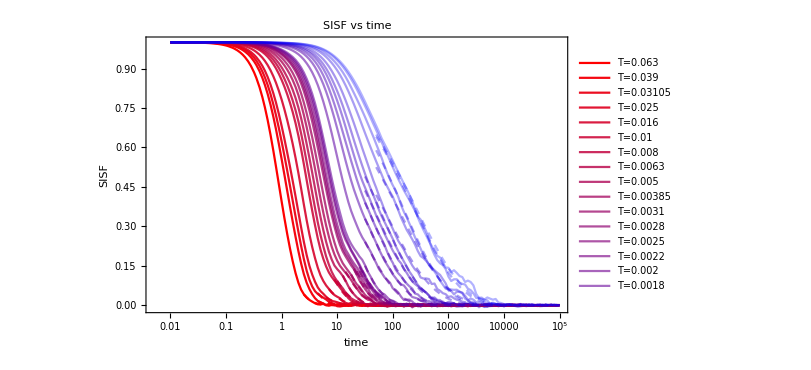

```mathematica
Show[SISFPlot,Table[LogLinearPlot[fitsSISF[[T]][x],{x,time[[fitSISFStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### Tau Alphas

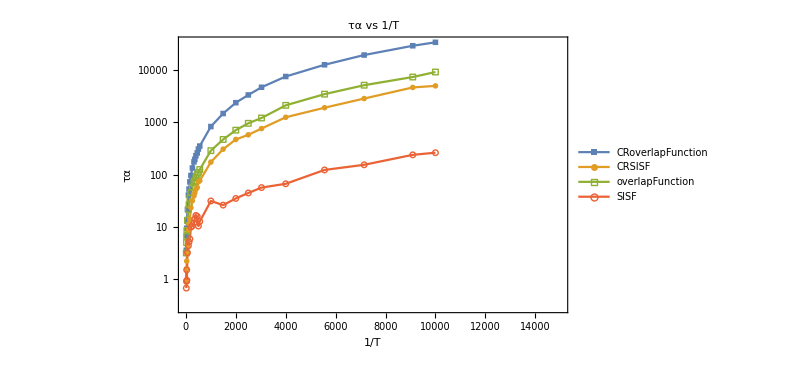

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCROverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauOverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■"],Style["●"],Style["□"],Style["○"]},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->{{0,15000},All}]
```

```mathematica
tauTable=Prepend[Table[{Tlist[[T]],tauCROverlapfits[[T]],tauCRSISFfits[[T]],tauOverlapfits[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}]
```

{{T,τα CRSISF,τα CR overlap,τα SISF,τα overlap},{0.063,3.64368,0.8786,3.1723,0.67436},{0.039,6.94708,1.58403,5.03112,0.911591},{0.03105,9.60145,2.21528,6.53628,1.50611},{0.025,13.2242,3.11014,8.6049,0.952369},{0.016,21.9273,4.28562,13.4784,3.21452},{0.01,41.593,8.7582,21.6783,4.3612},{0.008,53.9538,11.5562,26.7818,5.1447},{0.0063,74.0702,13.9348,35.3538,5.88111},{0.005,98.3638,23.3058,45.4896,9.89419},{0.00385,136.926,31.7959,58.014,10.5007},{0.0031,179.076,39.3313,71.0811,11.8835},{0.0028,200.318,45.0726,76.0834,14.2182},{0.0025,234.545,52.4653,86.8763,16.6049},{0.0022,266.116,56.897,101.324,15.9157},{0.002,315.354,73.2474,111.073,10.4152},{0.0018,359.787,76.8102,125.86,12.7049},{0.001,850.299,174.354,289.048,31.4613},{0.00067,1509.31,308.531,473.014,26.1893},{0.0005,2432.54,473.425,713.546,35.1702},{0.0004,3420.32,580.793,963.843,44.7117},{0.00033,4799.08,765.115,1219.08,56.7025}}

```mathematica
N[Table[1/(i*1000+10000),{i,1,5}]]
```

{0.0000909091,0.0000833333,0.0000769231,0.0000714286,0.0000666667}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP385.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP385.csv

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p385.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.890383,0.888215,0.898811,0.8992,0.888606,0.892447,0.898794,0.807516,0.899431,0.897256,0.897246,0.898543,0.844263,0.893645,0.899696,0.887575,0.822042,0.823415,0.791896,0.747604,0.673489}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.561604,0.561625,0.59677,0.59771,0.58893,0.501248,0.478341,0.511187,0.405287,0.406622,0.447637,0.429279,0.43632,0.456359,0.426028,0.450952,0.474974,0.482521,0.492746,0.530813,0.56397}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

Part::partd: Part specification fitsCRoverlap⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of fitsCRoverlap⟦1⟧[BestFitParameters] does not exist.

Part::partd: Part specification fitsCRoverlap⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of fitsCRoverlap⟦2⟧[BestFitParameters] does not exist.

Part::partd: Part specification fitsCRoverlap⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of fitsCRoverlap⟦3⟧[BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{fitsCRoverlap⟦1⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦2⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦3⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦4⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦5⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦6⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦7⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦8⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦9⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦10⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦11⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦12⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦13⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦14⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦15⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦16⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦17⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦18⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦19⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦20⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦21⟧[BestFitParameters]⟦3,2⟧}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

Part::partd: Part specification fitsCRoverlap⟦1⟧ is longer than depth of object.

Part::partd: Part specification fitsCRoverlap⟦1⟧[BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification fitsCRoverlap⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{fitsCRoverlap⟦1⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦2⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦3⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦4⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦5⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦6⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦7⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦8⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦9⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦10⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦11⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦12⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦13⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦14⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦15⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦16⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦17⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦18⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦19⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦20⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦21⟧[BestFitParameters]⟦1,2⟧}

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

tauCRSISFAllT

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

TlistAllT

```mathematica
TlistAllT
```

TlistAllT

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

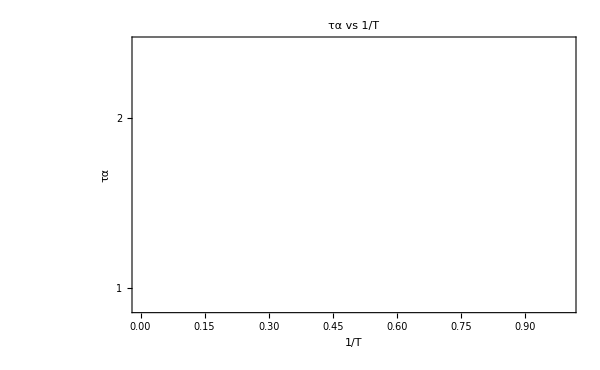

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

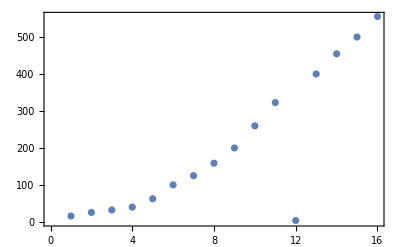

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16